## Initial Effort (No Neighbor List)

```mathematica
(* choose grid nxn size *)
```

```mathematica
n=5;
```

```mathematica
(* randomly initialize each cell *)
```

```mathematica
init=(SeedRandom[1997];RandomInteger[3,{n,n}]);
```

```mathematica
MatrixForm[init]
```

(1 | 3 | 3 | 3 | 3
0 | 0 | 1 | 1 | 1
2 | 3 | 0 | 2 | 2
1 | 1 | 1 | 0 | 3
0 | 2 | 2 | 1 | 3)

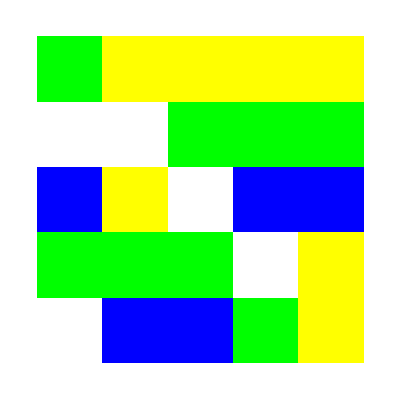

```mathematica
ArrayPlot[init,ColorRules->{0->White,1->Green,2->Blue,3->Yellow,4->Red}]
```

```mathematica
(* now take a step:*)
```

```mathematica
(* choose a position to add a grain *)
```

```mathematica
choice=First[(SeedRandom[1997];RandomSample[Flatten[Table[{i,j},{i,1,n},{j,1,n}],1],1])]
```

{4,1}

```mathematica
(* update initial config with new grain *)
```

```mathematica
init[[choice[[1]],choice[[2]]]]=init[[choice[[1]],choice[[2]]]]+1
```

2

```mathematica
MatrixForm@init
```

(1 | 3 | 3 | 3 | 3
0 | 0 | 1 | 1 | 1
2 | 3 | 0 | 2 | 2
2 | 1 | 1 | 0 | 3
0 | 2 | 2 | 1 | 3)

```mathematica
(* execute check for 4 grain  mounds *)
```

```mathematica
While[
MemberQ[Flatten[init],4],
Table[
Which[
init[[i,j]]<4,None
,
init[[i,j]]==4,
init[[i,j]]==init[[i,j]]-4;
Which[
i==1&&j==1,
init[[i+1,j]]=init[[i+1,j]]+1;
init[[i,j+1]]=init[[i,j+1]]+1;
,
i==n&&j==1,
init[[i-1,j]]=init[[i-1,j]]+1;
init[[i,j+1]]=init[[i,j+1]]+1;
,
i==n&&j==n,
init[[i,j-1]]=init[[i,j-1]]+1;
init[[i-1,j]]=init[[i-1,j]]+1;
,
i==1&&j==n,
init[[i,j-1]]=init[[i,j-1]]+1;
init[[i+1,j]]=init[[i+1,j]]+1;
,
(i>1&&i<n)&&(j>1&&j<n),
init[[i+1,j]]=init[[i+1,j]]+1;
init[[i,j+1]]=init[[i,j+1]]+1;
init[[i-1,j]]=init[[i-1,j]]+1;
init[[i,j-1]]=init[[i,j-1]]+1;
]
]
,{i,1,n},{j,1,n}]];
```

```mathematica
MatrixForm@init
```

(1 | 3 | 3 | 3 | 3
0 | 0 | 1 | 1 | 1
2 | 3 | 0 | 2 | 2
2 | 1 | 1 | 0 | 3
0 | 2 | 2 | 1 | 3)

```mathematica
(* let's choose a move that will topple things *)
```

```mathematica
choice2={1,2};
```

```mathematica
initList={init};
```

```mathematica
init[[choice2[[1]],choice2[[2]]]]=init[[choice2[[1]],choice2[[2]]]]+1
```

4

```mathematica
AppendTo[initList,init];
```

```mathematica
MatrixForm@init
```

(1 | 4 | 3 | 3 | 3
0 | 0 | 1 | 1 | 1
2 | 3 | 0 | 2 | 2
1 | 1 | 1 | 0 | 3
0 | 2 | 2 | 1 | 3)

```mathematica
While[
MemberQ[Flatten[init],4],
Table[
Which[
init[[i,j]]<4,None
,
init[[i,j]]==4,
init[[i,j]]==init[[i,j]]-4;
Which[
i==1&&j==1,
init[[i+1,j]]=init[[i+1,j]]+1;
init[[i,j+1]]=init[[i,j+1]]+1;
,
i==n&&j==1,
init[[i-1,j]]=init[[i-1,j]]+1;
init[[i,j+1]]=init[[i,j+1]]+1;
,
i==n&&j==n,
init[[i,j-1]]=init[[i,j-1]]+1;
init[[i-1,j]]=init[[i-1,j]]+1;
,
i==1&&j==n,
init[[i,j-1]]=init[[i,j-1]]+1;
init[[i+1,j]]=init[[i+1,j]]+1;
,
(i>1&&i<n)&&(j>1&&j<n),
init[[i+1,j]]=init[[i+1,j]]+1;
init[[i,j+1]]=init[[i,j+1]]+1;
init[[i-1,j]]=init[[i-1,j]]+1;
init[[i,j-1]]=init[[i,j-1]]+1;
]
];
AppendTo[initList,init];
,{i,1,n},{j,1,n}]];
```

$Aborted

## Faster (Mapping Grid-Check, Neighbor Lists)

```mathematica
(* choose grid nxn size *)
```

```mathematica
n=5;
```

```mathematica
(* randomly initialize each cell *)
```

```mathematica
init=(SeedRandom[1997];RandomInteger[3,{n,n}]);
```

```mathematica
MatrixForm[init]
```

(1 | 3 | 3 | 3 | 3
0 | 0 | 1 | 1 | 1
2 | 3 | 0 | 2 | 2
1 | 1 | 1 | 0 | 3
0 | 2 | 2 | 1 | 3)

```mathematica
ArrayPlot[init,ColorRules->{0->White,1->Green,2->Blue,3->Yellow,4->Red}]
```

-Graphics-

```mathematica
(* save this initial config *)
```

```mathematica
initList={init};
```

```mathematica
(* make a list of each entry for mapping: *)
```

```mathematica
gridInds=Flatten[Table[{i,j},{i,1,n},{j,1,n}],1];
```

```mathematica
gridInds
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}}

```mathematica
(* make a neighbor association *)
```

```mathematica
neighbors[choice_,n_]:=Module[{i,j,neighbList={}},
i=choice[[1]];
j=choice[[2]];
Which[
i==1&&j==1,(*good*)
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i+1,j}];
,
i==n&&j==1,(*good*)
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i,j+1}];
,
i==n&&j==n,(*good*)
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i,j-1}];
,
i==1&&j==n,(*good*)
AppendTo[neighbList,{i,j-1}];
AppendTo[neighbList,{i+1,j}];
,
i==1&&(j>1&&j<n),(*good*)
AppendTo[neighbList,{i,j-1}];
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i+1,j}];
,
i==n&&(j>1&&j<n),(*good*)
AppendTo[neighbList,{i,j-1}];
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i-1,j}];
,
(i>1&&i<n)&&j==1,(*good*)
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i+1,j}];
,
(i>1&&i<n)&&j==n,(*good*)
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i+1,j}];
AppendTo[neighbList,{i,j-1}];
,
(i>1&&i<n)&&(j>1&&j<n),
AppendTo[neighbList,{i,j-1}];
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i+1,j}];
];
{choice,neighbList}
]
```

```mathematica
neighbs=Map[neighbors[#,n]&,gridInds];
```

```mathematica
(* make a random choice *)
```

```mathematica
choice=First[(SeedRandom[1997];RandomSample[Flatten[Table[{i,j},{i,1,n},{j,1,n}],1],1])]
```

{4,1}

```mathematica
(* update the initial grid with  *)
```

```mathematica
init[[choice[[1]],choice[[2]]]]=init[[choice[[1]],choice[[2]]]]+1
```

2

```mathematica
AppendTo[initList,init];
```

```mathematica
(* execute check for avalanches *)
```

```mathematica
While[MemberQ[Flatten[init],4],
Map[
Which[
init[[#[[1]][[1]],#[[1]][[2]]]]<4,
None
,
init[[#[[1]][[1]],#[[1]][[2]]]]==4,
init[[#[[1]][[1]],#[[1]][[2]]]]=init[[#[[1]][[1]],#[[1]][[2]]]]-4;
Table[init[[#[[2]][[i]][[1]],#[[2]][[i]][[2]]]]=init[[#[[2]][[i]][[1]],#[[2]][[i]][[2]]]]+1,{i,1,Length[#[[2]]]}];
]&,neighbs];
AppendTo[initList,init];
]
```

```mathematica
MatrixForm@init
```

(1 | 3 | 3 | 3 | 3
0 | 0 | 1 | 1 | 1
2 | 3 | 0 | 2 | 2
2 | 1 | 1 | 0 | 3
0 | 2 | 2 | 1 | 3)

```mathematica
(* make a choice that does cause an avalanche: *)
```

```mathematica
choice={1,2};
```

```mathematica
init[[choice[[1]],choice[[2]]]]=init[[choice[[1]],choice[[2]]]]+1
```

4

```mathematica
MatrixForm@init
```

(1 | 4 | 3 | 3 | 3
0 | 0 | 1 | 1 | 1
2 | 3 | 0 | 2 | 2
2 | 1 | 1 | 0 | 3
0 | 2 | 2 | 1 | 3)

```mathematica
(* execute check for avalanches *)
```

```mathematica
While[MemberQ[Flatten[init],4],
Map[
Which[
init[[#[[1]][[1]],#[[1]][[2]]]]<4,
None
,
init[[#[[1]][[1]],#[[1]][[2]]]]==4,
init[[#[[1]][[1]],#[[1]][[2]]]]=init[[#[[1]][[1]],#[[1]][[2]]]]-4;
Table[init[[#[[2]][[i]][[1]],#[[2]][[i]][[2]]]]=init[[#[[2]][[i]][[1]],#[[2]][[i]][[2]]]]+1,{i,1,Length[#[[2]]]}];
]&,neighbs];
AppendTo[initList,init];
]
```

```mathematica
ListAnimate[Map[ArrayPlot[#,ColorRules->{0->White,1->Green,2->Blue,3->Yellow,4->Red}]&,initList]]
```

## Functionalize w/ Faster Implementation

```mathematica
(* makes a neighbor list for a given cell and grid size *)
```

```mathematica
neighbors[choice_,n_]:=Module[{i,j,neighbList={}},
i=choice[[1]];
j=choice[[2]];
Which[
i==1&&j==1,(*good*)
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i+1,j}];
,
i==n&&j==1,(*good*)
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i,j+1}];
,
i==n&&j==n,(*good*)
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i,j-1}];
,
i==1&&j==n,(*good*)
AppendTo[neighbList,{i,j-1}];
AppendTo[neighbList,{i+1,j}];
,
i==1&&(j>1&&j<n),(*good*)
AppendTo[neighbList,{i,j-1}];
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i+1,j}];
,
i==n&&(j>1&&j<n),(*good*)
AppendTo[neighbList,{i,j-1}];
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i-1,j}];
,
(i>1&&i<n)&&j==1,(*good*)
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i+1,j}];
,
(i>1&&i<n)&&j==n,(*good*)
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i+1,j}];
AppendTo[neighbList,{i,j-1}];
,
(i>1&&i<n)&&(j>1&&j<n),
AppendTo[neighbList,{i,j-1}];
AppendTo[neighbList,{i,j+1}];
AppendTo[neighbList,{i-1,j}];
AppendTo[neighbList,{i+1,j}];
];
{choice,neighbList}
]
```

```mathematica
(* run avalanche given an initial configuration and number of random additions *)
```

```mathematica
avalanche[initialCfg_,nsteps_]:=Module[{icfg,size,list,choice,gInds,ne},
icfg=initialCfg;
size=Length[initialCfg[[1]]];
gInds=Flatten[Table[{i,j},{i,1,size},{j,1,size}],1];
list={icfg};
ne=Map[neighbors[#,size]&,gInds];
Do[
choice=First[RandomSample[Flatten[Table[{i,j},{i,1,size},{j,1,size}],1],1]];
icfg[[choice[[1]],choice[[2]]]]=(icfg[[choice[[1]],choice[[2]]]]+1);
AppendTo[list,icfg];
While[MemberQ[GreaterThan[3]/@Flatten[icfg],True],
Map[
Which[
icfg[[#[[1]][[1]],#[[1]][[2]]]]<4,
None
,
icfg[[#[[1]][[1]],#[[1]][[2]]]]>=4,
icfg[[#[[1]][[1]],#[[1]][[2]]]]=icfg[[#[[1]][[1]],#[[1]][[2]]]]-4;
Table[icfg[[#[[2]][[i]][[1]],#[[2]][[i]][[2]]]]=icfg[[#[[2]][[i]][[1]],#[[2]][[i]][[2]]]]+1,{i,1,Length[#[[2]]]}];
]&,ne];
AppendTo[list,icfg];
]
,nsteps];
list
]
```

```mathematica
run25=avalanche[(SeedRandom[1997];RandomInteger[3,{25,25}]),50];
```

```mathematica
ListAnimate[Map[ArrayPlot[#,ColorRules->{0->White,1->Green,2->Blue,3->Yellow,4->Red}]&,run25]]
```

```mathematica
check=((3*Table[(-1)^(row+col),{row,1,25},{col,1,25}])/.{-3->0});
```

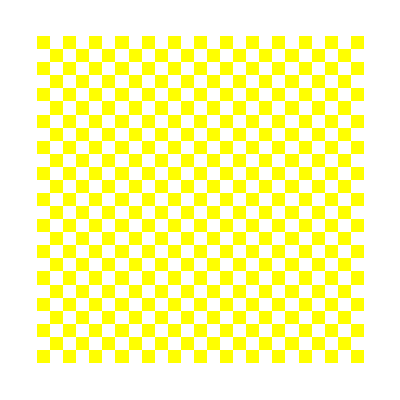

```mathematica
ArrayPlot[check,ColorRules->{0->White,1->Green,2->Blue,3->Yellow,4->Red}]
```

```mathematica
run25check=avalanche[check,1000];
```

```mathematica
ListAnimate[Map[ArrayPlot[#,ColorRules->{0->White,1->Green,2->Blue,3->Yellow,4->Red}]&,run25check]]
```

```mathematica
even3=((3*Table[(1)^(row+col),{row,1,25},{col,1,25}]));
```

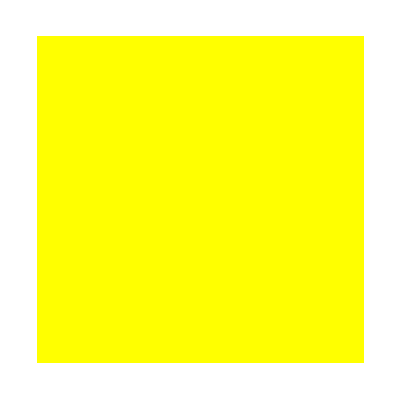

```mathematica
ArrayPlot[even3,ColorRules->{0->White,1->Green,2->Blue,3->Yellow,4->Red}]
```

```mathematica
runEven3=avalanche[even3,100];
```

```mathematica
ListAnimate[Map[ArrayPlot[#,ColorRules->{0->White,1->Green,2->Blue,3->Yellow,4->Red}]&,runEven3]]
```